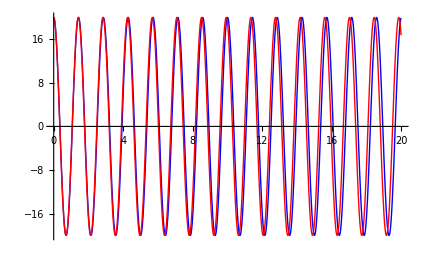
```mathematica
g=9.8;
 
(*grav. constant*)
l=0.5; (*length of pendulum*)

θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0};
sol=NDSolve[ode1,θ,{t,0,20}];
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];

Show[{myplot1,myplot2}]
-Graphics-
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

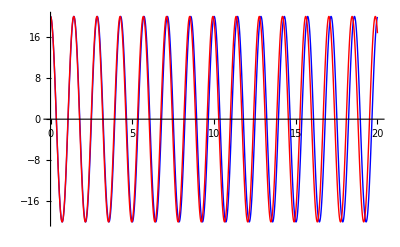

-Graphics-

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.1, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.1, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
(*g = 9.8 (*m/s^2*)*)
vt=100
v =30
θ=50 π/180

ode1 ={x''[t]==(-g x'[t]/ vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t]==-g(1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==0,y[0]==2, x'[0]== v*Cos[θ], y'[0]==v*Sin[θ]}
```

100

30

(5 π)/18

{x''[t]==-0.00098 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/10000),x[0]==0,y[0]==2,x'[0]==30 Sin[(2 π)/9],y'[0]==30 Cos[(2 π)/9]}

```mathematica
(*ode2 ={x''[t]==-0.32666666666666666 t^2 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+1/30 t^2 y'[t] √(x'[t]^2+y'[t]^2)),x[0]==0,y[0]==2,x'[0]==30 ,y'[0]==30 }*) (*she was trying to fix my code and this came up*)
```

```mathematica
sol=NDSolve[ode1, {x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

NDSolve::ndinnt: Initial condition 30.\ Cos[0.277778\ pi] is not a number or a rectangular array of numbers.

ox[{

       RowBox[{"\[Theta]", "'"}], "[", "0", "]"}], "\[Equal]", 

      "\[Omega]0"}]}], "}"}]}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"sol", "=", 

   RowBox[{"NDSolve", "[", 

    RowBox[{"ode1", ",", "\[Theta]", ",", 

     RowBox[{"{", 

      RowBox[{"t", ",", "0", ",", "20"}], "}"}]}], "]"}]}], ";"}], "\n", 

 RowBox[{

  RowBox[{"myplot1", " ", "=", " ", 

   RowBox[{"Plot", "[", 

    RowBox[{

     RowBox[{

      RowBox[{

       RowBox[{"(", 

        RowBox[{"180", "/", "Pi"}], ")"}], " ", 

       RowBox[{"\[Theta]", "[", "t", "]"}]}], "/.", "sol"}], ",", 

     RowBox[{"{", 

      RowBox[{"t", ",", "0", ",", "20"}], "}"}], ",", 

     RowBox[{"PlotStyle", "\[Rule]", " ", 

      RowBox[{"RGBC

NDSolve[{x''[t]==-0.326667 t^2 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+1/30 t^2 y'[t] √(x'[t]^2+y'[t]^2)),x[0]==0,y[0]==2,x'[0]==30 Cos[(5 pi)/18],y'[0]==30 Sin[(5 pi)/18]},{x,y},{t,0,100}]

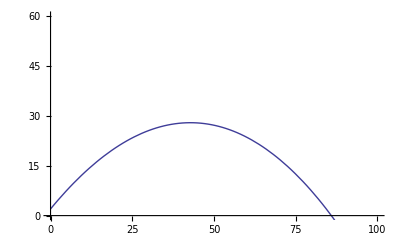

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t, 0, 200}, PlotRange->{{0,100},{0,60}}]
```

```mathematica
Manipulate [ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t, 0, tf}, PlotRange->{{0,100},{0,60}}],{{tf,0.01,"time(s)"},0.01,100, Appearance->"Labeled"}, {{v,0.01,"Velocity(m/s)"},0.01,30, Appearance->"Labeled"},{{g,0.01,"Gravity(m/s^s"}, 0.01,9.8, Appearance->"Labeled"},{{θ,0.01,"θ(rad/s)"},0.01,π , Appearance->"Labeled"}]
```